# Examen 1: Parte Computacional Sistemas Dinámicos No Lineales

## Profesor: Josué Manik Nava Sedeño Alumno: Wei Le Hu Tang 25 de febrero del 2024

Elabora un notebook en el software mathematica respondiendo TODAS las preguntas. Para cada inciso interpreta lo que se esté analizando y escribelo en lenguaje natural. Dicha interpretación representa la MITAD del porcentaje de la calificación. (NO se contará ninguna interpretación sin argumento matemático y/o computacional)

Considera el modelo para poblaciones con mínimo de individuos:

(a) Encuentra las soluciones de la ecuación diferencial para 3 diferentes condiciones inciales cualitativamente distintas.

Nótense varias cosas antes de empezar:
- Este es un modelo poblacional, entonces no tiene sentido considerar poblaciones negativas, por lo que .
-  y  son el máximo y el mínimo poblacional, respectivamente, por lo que , y considerando :
	- si , entonces , no existe suficiente población para aumentar, pero sí para mantenerse estable.
	- si , entonces , se ha alcanzado la capacidad de carga, ya no puede aumentar para por la falta de recursos (territoriales o alimenticios).
	- si , entonces , sin deficiencias reproductivas, hay suficientes individuos para crecimiento poblacional, hasta ya no poder, es decir va a tender a .
	- si , entonces , al sobrepasar la capacidad de carga, la falta de recursos causará un decrecimiento poblacional hasta estabilizarse.
	- si , entonces , no existen suficientes ejemplares para reproducción y hacer crecer la población, entonces ésta se empieza a extinguir.
-   es la tasa de reproducción, tal que:
	- si , entonces , lo que indica un equilibrio reproductivo independiente de la población, esta se mantiene constante: nace uno, muere uno.
	- si , existe una deficiencia reproductiva, pero tomando en cuenta las desigualdades de :
		- si , apesar de estar en un intervalo seguro, la población decrece a causa de la deficienica reproductiva.
		- si , se ha sobrepasado la capacidad de carga, entonces no tiene sentido que siga creciendo.
		- si , aunque hay menor población que la mínima necesaria, ésta crece, lo cual no tiene sentido.
	- si , la reproducción es eficiente, y los casos posibles son los últimos tres presentados para las desigualdades de .
	- como  no es interés de estudio y  no tiene sentido en el contexto de poblaciones de especies, entonces se considerará únicamente .
Entonces:




En particular, se tomarán los siguientes parámetros:

```mathematica
clearAll[r,M,m,P];
M=100;
m=10;
r=.01;
```

Caso 1:

```mathematica
sol1=DSolve[{P'[t]==r*(M-P[t])*(P[t]-m), P[0]==15},P,t];
sol1
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P→Function[{t},(100. ((1.7+1.30171×10^-15 ⅈ)+1. 2.71828^(0.9 t)))/((17.+1.30171×10^-14 ⅈ)+2.71828^(0.9 t))]}}

Caso 2:

```mathematica
sol2=DSolve[{P'[t]==r*(M-P[t])*(P[t]-m), P[0]==120},P,t];
sol2
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P→Function[{t},(100. (-0.0181818+1. 2.71828^(0.9 t)))/(-0.181818+2.71828^(0.9 t))]}}

Caso 3:

```mathematica
sol3=DSolve[{P'[t]==r*(M-P[t])*(P[t]-m), P[0]==9},P,t];
sol3
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{P→Function[{t},(100. (-9.1+1. 2.71828^(0.9 t)))/(-91.+2.71828^(0.9 t))]}}

(b) Grafica los planos ,  ̇y ,  para las mismas condiciones iniciales y explica la relación que hay entre los planos usando sus características cualitativas como referencia.

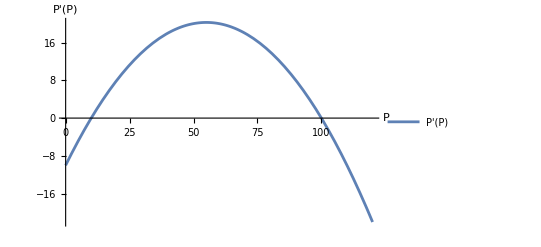

```mathematica
Plot[r(M-p)(p-m),{p,0,120},PlotLegends->{"P'(P)"},AxesLabel->{"P","P'(P)"}]
```

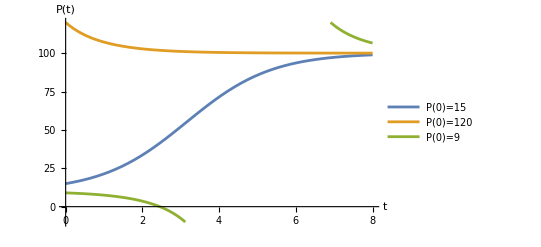

```mathematica
P1[t_]=P[t]/. sol1;
P2[t_]=P[t]/. sol2;
P3[t_]=P[t]/. sol3;

Plot[{P1[t],P2[t],P3[t]},{t,0,8},PlotLegends->{"P(0)=15","P(0)=120","P(0)=9"},PlotRange->{{0,8},{-10,120}}, AxesLabel->{"t","P(t)"}]
```

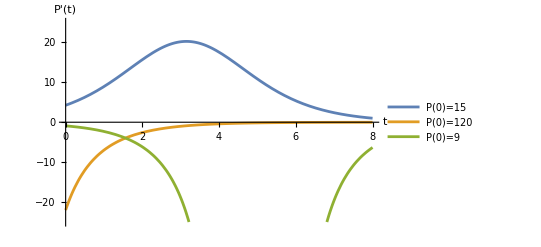

```mathematica
Pdot1[t_]=P'[t]/. sol1;
Pdot2[t_]=P'[t]/. sol2;
Pdot3[t_]=P'[t]/. sol3;

Plot[{Pdot1[t],Pdot2[t],Pdot3[t]},{t,0,8},PlotLegends->{"P(0)=15","P(0)=120","P(0)=9"},PlotRange->{{0,8},{-25,25}},AxesLabel->{"t","P'(t)"}]
```

Caso 1: 

Se presenta un crecimiento logístico, en el que la velocidad aumenta hasta aproximadamente  donde si bien sigue creciendo la velocidad empieza a disminuir, por eso la gráfica de  parece una campana, pero siempre es positiva. Después  tiende a  cuando  tiende a , indicando que se está llegando al máximo poblacional o capacidad de carga. Asímismo se puede notar que  es positiva en este intervalo, lo que indica que es estríctamente creciente, y , esto mismo indica que  tiende asintóticamente a .

Caso 2: 

Por la condición inicial, , ya que la población sobrepasa la capacidad de carga, entonces decrece hasta volver a  que es justo donde  tiene raíz, misma función que parmanece negativa en el intervalo de . Este comportamiento decreciente se puede ver en la gráfica de ; al igual que se puede notar el cambio de pendiente en , donde inicia negativo y crece hasta llegar asintóticamente a , que es cuando  va convergiendo a .

Caso 3: 

Al no tener la población mínima, la especie tiende a la extinción, nótese que tanto  como  son cada vez más negativas, lo que implica una desventaja para este modelo pues, como se puede ver cuando  es aproximadamente , , pero éste sigue decreciendo a poblaciones negativas, que no tiene sentido real.

(c) Fija dos de los parámetros de la ecuación y explica el comportamiento del sistema en términos del parámetro faltante. (deben ser 3 análisis distintos)

Retomando el inciso a), mantendremos:





Caso 1: Fijando

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

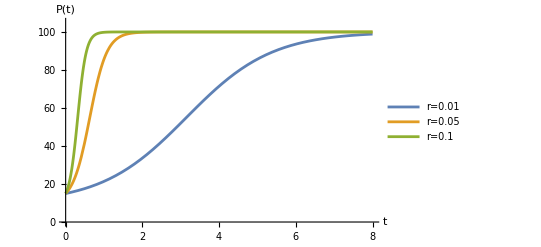

```mathematica
M=100;
m=10;
r1=0.01;
r2=0.05;
r3=0.1;

sol1=DSolve[{P'[t]==r1*(M-P[t])*(P[t]-m), P[0]==15},P,t];
sol2=DSolve[{P'[t]==r2*(M-P[t])*(P[t]-m), P[0]==15},P,t];
sol3=DSolve[{P'[t]==r3*(M-P[t])*(P[t]-m), P[0]==15},P,t];

P1[t_]=P[t]/. sol1;
P2[t_]=P[t]/. sol2;
P3[t_]=P[t]/. sol3;

Plot[{P1[t],P2[t],P3[t]},{t,0,8},PlotLegends->{"r=0.01","r=0.05","r=0.1"},PlotRange->{{0,8},{0,105}}, AxesLabel->{"t","P(t)"}]
```

Dadas  y , la rapidez en la que la población converge a la capacidad de carga es proporcional al aumento de , la tasa de reproducción.

Caso 2: Fijando

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

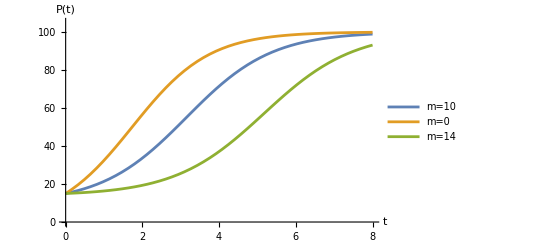

```mathematica
M=100;
r=0.01;
m1=10;
m2=0;
m3=14;

sol1=DSolve[{P'[t]==r*(M-P[t])*(P[t]-m1), P[0]==15},P,t];
sol2=DSolve[{P'[t]==r*(M-P[t])*(P[t]-m2), P[0]==15},P,t];
sol3=DSolve[{P'[t]==r*(M-P[t])*(P[t]-m3), P[0]==15},P,t];

P1[t_]=P[t]/. sol1;
P2[t_]=P[t]/. sol2;
P3[t_]=P[t]/. sol3;

Plot[{P1[t],P2[t],P3[t]},{t,0,8},PlotLegends->{"m=10","m=0","m=14"},PlotRange->{{0,8},{0,105}}, AxesLabel->{"t","P(t)"}]
```

Al disminuír la población mínima, en este ejemplo , aumenta el crecimiento inicial, porque este requisito también significa que entre más cerca se esté de , menor es la reproducción (se puede apreciar en el caso de ), y análogamente, mientras mayor sea a comparación de , más fácil es la reproducción, pues no se encuentran en niveles críticos.

Caso 3: Fijando

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

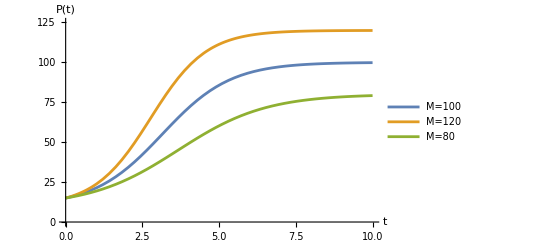

```mathematica
m=10;
r=0.01;
M1=100;
M2=120;
M3=80;

sol1=DSolve[{P'[t]==r*(M1-P[t])*(P[t]-m), P[0]==15},P,t];
sol2=DSolve[{P'[t]==r*(M2-P[t])*(P[t]-m), P[0]==15},P,t];
sol3=DSolve[{P'[t]==r*(M3-P[t])*(P[t]-m), P[0]==15},P,t];

P1[t_]=P[t]/. sol1;
P2[t_]=P[t]/. sol2;
P3[t_]=P[t]/. sol3;

Plot[{P1[t],P2[t],P3[t]},{t,0,10},PlotLegends->{"M=100","M=120","M=80"},PlotRange->{{0,10},{0,125}}, AxesLabel->{"t","P(t)"}]
```

Cuando se tienen capacidades de carga más grandes, se converge más rápido, pues aunque la población máxima aumente, eso también permite un punto de inflexión con mayor pendiente (un pico de aumento poblacional más alto).

(d) Fija la tasa de crecimineto  y varia las cotas  y . Explica el comportamiento de la población para dicho casos.
Mantiendo:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

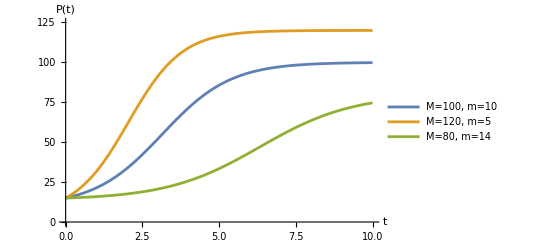

```mathematica
r=0.01;
M1=100;
m1=10;
M2=120;
m2=5;
M3=80;
m3=14;

sol1=DSolve[{P'[t]==r*(M1-P[t])*(P[t]-m1), P[0]==15},P,t];
sol2=DSolve[{P'[t]==r*(M2-P[t])*(P[t]-m2), P[0]==15},P,t];
sol3=DSolve[{P'[t]==r*(M3-P[t])*(P[t]-m3), P[0]==15},P,t];

P1[t_]=P[t]/. sol1;
P2[t_]=P[t]/. sol2;
P3[t_]=P[t]/. sol3;

Plot[{P1[t],P2[t],P3[t]},{t,0,10},PlotLegends->{"M=100, m=10","M=120, m=5","M=80, m=14"},PlotRange->{{0,10},{0,125}}, AxesLabel->{"t","P(t)"}]
```

Al aumentar la distancia entre  y , dada una  fija, el crecimiento poblacional también es mayor, y viceversa. Esto se debe a que mayor capacidad de carga () implica mayor disponibilidad de recursos, y menor población crítica () implica mayor facilidad de reproducción.

(e) Haz un análisis en términos de la longitud  y la tasa de crecimiento  en el sistema. ¿Qué sucede cuando uno crece y el otro disminuye? ¿Qué pasa cuando ambos crecen? ¿Qué sucede cuando fijas uno y varías el otro?

Aparte de lo visto en el inciso anterior:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

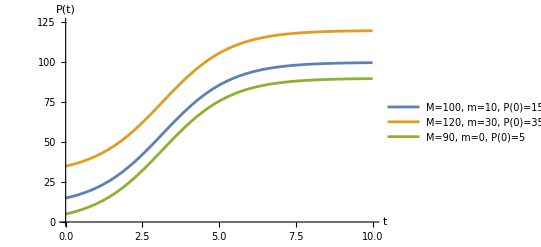

```mathematica
r=0.01;
M1=100;
m1=10;
M2=120;
m2=30;
M3=90;
m3=0;

sol1=DSolve[{P'[t]==r*(M1-P[t])*(P[t]-m1), P[0]==15},P,t];
sol2=DSolve[{P'[t]==r*(M2-P[t])*(P[t]-m2), P[0]==35},P,t];
sol3=DSolve[{P'[t]==r*(M3-P[t])*(P[t]-m3), P[0]==5},P,t];

P1[t_]=P[t]/. sol1;
P2[t_]=P[t]/. sol2;
P3[t_]=P[t]/. sol3;

Plot[{P1[t],P2[t],P3[t]},{t,0,10},PlotLegends->{"M=100, m=10, P(0)=15","M=120, m=30, P(0)=35","M=90, m=0, P(0)=5"},PlotRange->{{0,10},{0,125}}, AxesLabel->{"t","P(t)"}]
```

Nótese que dadas , , y  fijas, las gráficas son iguales, lo que nos indica que el crecimiento poblacional tiene cierta dependencia especial entre estos parámetros. 
Entonces fijar  y variar , es equivalente al análisis hecho cuando se fijaron  y  y se varió  en el Caso 1 del inciso anterior, pues como ya se vió, la función depende más de la distancia entre estos dos parámetros que de realmente cuáles son.
Mientras que  y variar , es equivalente a los Casos 2 y 3 del inciso anterior, donde se puede apreciar, que al aumentar la diferencia reduciendo  o incrementando , provoca un crecimiento más rápido, dada una condición inicial; mientras que análogamente, reduciendo la diferencia crea un efecto opuesto.

Ahora sea 
La ecuación queda: 
Fijando:

70

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

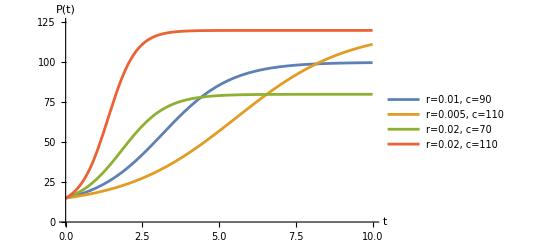

```mathematica
m=10;
r1=0.01;
c1=90;
r2=0.005;
c2=110;
r3=0.02;
c3=70
r4=0.02;
c4=110;

sol1=DSolve[{P'[t]==r1*((m+c1)-P[t])*(P[t]-m), P[0]==15},P,t];
sol2=DSolve[{P'[t]==r2*((m+c2)-P[t])*(P[t]-m), P[0]==15},P,t];
sol3=DSolve[{P'[t]==r3*((m+c3)-P[t])*(P[t]-m), P[0]==15},P,t];
sol4=DSolve[{P'[t]==r4*((m+c4)-P[t])*(P[t]-m), P[0]==15},P,t];

P1[t_]=P[t]/. sol1;
P2[t_]=P[t]/. sol2;
P3[t_]=P[t]/. sol3;
P4[t_]=P[t]/. sol4;

Plot[{P1[t],P2[t],P3[t],P4[t]},{t,0,10},PlotLegends->{"r=0.01, c=90","r=0.005, c=110","r=0.02, c=70","r=0.02, c=110"},PlotRange->{{0,10},{0,125}}, AxesLabel->{"t","P(t)"}]
```

Cuando  crece y  disminuye, se tarda más en llegar a , pues hay menor tasa de reproducción y mayor límite poblacional; análogamente, si  disminuye y  crece, se llega más rápido a , pues la tasa de reproducción aumenta pero la capacidad de carga es menor, entonces se satura más rápido el entorno donde se encuentra la especie.
Por otro lado, si ambos aumentan, crea un crecimiento aun más pronunciado, pues tanto hay mayores recursos, como hay mejor eficiencia reproductiva.

(f) (Extra) Usando el método de separación de variables y haciendo fracciones parciales en un lado de la igualdad resuelve la ecuacion diferencial y relaciona el inciso anteriror con dicha solución.


Usando fracciones parciales:










Regresando:



Tómese  como constante que “absorbe otras constantes” sin cambiar notación, por conveniencia

Considera el modelo de propagación de infecciones dado por el siguiente
sistema dinámico

(a) Grafica el retrato fase del sistema en 2 dimensiones con 2 parejas de parámetros cualitativamente distintas.

Nótse que , porque son la tasa de infección y recuperación, respectivamente:

Caso 1:

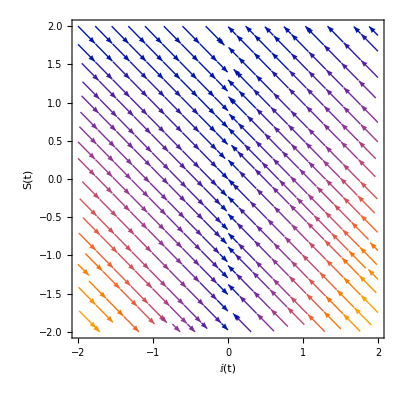

```mathematica
bet=0.3;
gam=0.6;
f[i_,s_]:={bet*s*i-gam*i,-bet*s*i+gam*i};
StreamPlot[f[i,s],{i,-2,2},{s,-2,2},FrameLabel->{I[t],S[t]}]
```

Caso 1:

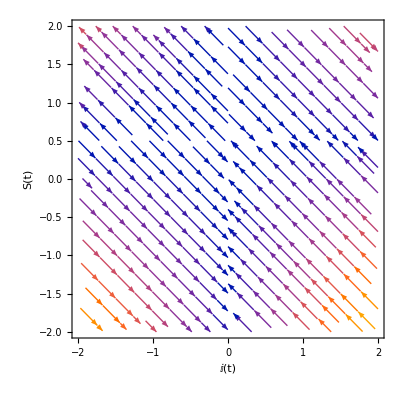

```mathematica
bet=0.6;
gam=0.3;
f[i_,s_]:={bet*s*i-gam*i,-bet*s*i+gam*i};
StreamPlot[f[i,s],{i,-2,2},{s,-2,2},FrameLabel->{I[t],S[t]}]
```

(b) Encuentra las soluciones de la reducción del sistema a la variable  y relacionalo con el modelo del ejercicio 1 identificando los parámetros nuevos.
Sea 

Entonces , la población total, es constante, tal que 



Análogamente al modelo poblacional, en este caso se tiene que:
	, la máxima cantidad de susceptibles es la población total, intuitivamente..08 Este mismo número es un punto de equilibrio, pues cuando , es decir: si todos están sanos, nadie se puede infectar de la nada.
	, es la población mínima de susceptibles, por así decirlo, igualmente si , lo que es que si la cantidad de susceptibles es proporcional a la relación entre la probabilidad de recuperación y la de infección, entonces ésta se mantiene.
	, entonces se tendría el análisis de casos para  que se hizo en el ejercicio 1, que en este contexto tiene más sentido, pues si: , significa que sí existen infectados y la población de susceptibles es suficientemente grande como para infectarse y disminuir, hasta llegar punto donde la tasa de infección y la de curación se equilibren, es decir, cuando ; sin embargo, si  entonces las personas suceptibles son tan pocas que tienden a recuperarse más rápido de lo que se infecta alguien, volviendo a la función creciente y tendiendo al punto de equilibrio  de nuevo. El tercer caso, donde  sigue sin hacer sentido aquí, pues no pueden haber más que la población total.

Tómense:


 (Un modelo normalizado, donde se verá la población en proporciones o porcentajes)

```mathematica
bet=0.6;
gam=0.3;
T=1; (*Se usó T en lugar de N, porque el símbolo N está protegido*)
sol=DSolve[S'[t]==-bet*(S[t]-gam/bet)*(T-S[t]),S,t];
sol
```

{{S→Function[{t},(-1.+2.71828^(0.3 t+C[1]))/(-1.+2. 2.71828^(0.3 t+C[1]))]}}

(c) Grafica e interpreta el comportamiento de la variable  para 3 condiciones iniciales cualitativamente distintas.

Recuérde que , y 

Caso 1:

```mathematica
sol1=DSolve[{S'[t]==-bet*(S[t]-gam/bet)*(T-S[t]),S[0]==7/8},S,t];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Caso 2:

```mathematica
sol2=DSolve[{S'[t]==-bet*(S[t]-gam/bet)*(T-S[t]),S[0]==1/8},S,t];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Caso 3:

```mathematica
sol3=DSolve[{S'[t]==-bet*(S[t]-gam/bet)*(T-S[t]),S[0]==1.1},S,t];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

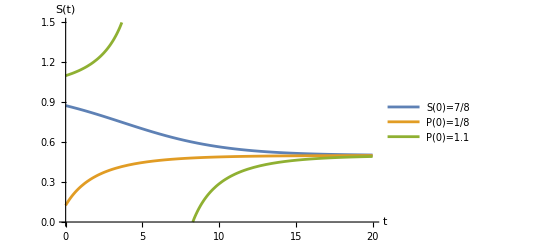

```mathematica
S1[t_]=S[t]/. sol1;
S2[t_]=S[t]/. sol2;
S3[t_]=S[t]/. sol3;

Plot[{S1[t],S2[t],S3[t]},{t,0,20},PlotLegends->{"S(0)=7/8","P(0)=1/8","P(0)=1.1"},PlotRange->{{0,20},{0,1.5}}, AxesLabel->{"t","S(t)"}]
```

Nótese que  es un punto de equilibrio inestable, pues con que haya algún infectado, la población de susceptibles decrece; mientras que  es un punto de equilibrio estable, pues es el punto en el que por la proporciones de la población, se contagian tantos como se recuperan, aparte de que si hay pocos susceptibles, se recuperan más de lo que se contagian, tendiendo al equilibrio, y viceversa. Sin embargo, como se comentó anteriormente, el Caso 3, no es de relevancia, pues no puede haber mayor población que la total, aunque algo rescatable de ahí es que a pesar de haber 0 susceptibles (es decir, están todos contagiados) en algún momento, estos sí se pueden recuperar.